# Minimalizace, Lagrangeovy multiplikátory a Newtonova metoda

## Ostrovy - aneb dlouho očekávané setkání na mostě Srdečných a Amébovitých

## Jak vypadají ostrovy našich obyvatel? (Překvapení!!! Jako jejich obyvatelé.)

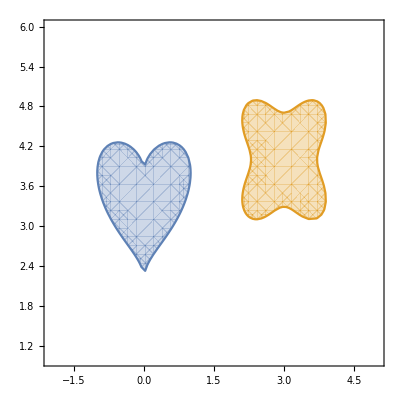

```mathematica
mapa =RegionPlot[{x^2+(5(y-3)/4-Sqrt[Abs[x]])^2 ≤ 1,(2(x-3)^2+2(y-4)^2)^3-40(x-3)^2 *(y-4)^2 ≤ 1},{x,-2,5},{y,1,6}]
```

## Výpočet - Jak postavit most mezi národy?

```mathematica
ϵ=0.001
g1=x1^2+(5(x2-3)/4-(x1^2+ϵ^2)^(1/4))^2;
g2=(2(y1-3)^2+2(y2-4)^2)^3-40(y1-3)^2 *(y2-4)^2;
f = (x1-y1)^2 + (x2-y2)^2;
smallLagrangian= Piecewise[{{-λ^2 /(2ρ),λ+ρ*g ≤ ρ},{λ(g-1)+ρ/2 (g-1)^2,λ+ρ*g > ρ}}];
```

0.001

```mathematica
Lagrangian = f + ReplaceAll[ReplaceAll[smallLagrangian,g->g1],λ->λ1]+ReplaceAll[ReplaceAll[smallLagrangian,g->g2],λ->λ2];
```

```mathematica
DfDx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2}} ];
D2fDxx=D[ Lagrangian,{{x1,x2,y1,y2,λ1,λ2},2} ];
ρ=0.001;
```

```mathematica
{x1,x2,y1,y2,λ1,λ2}={1.,4.,2.,3.,0.,0.};
i=0;
history1={{x1,x2}};
history2={{y1,y2}};
While[ Sqrt[DfDx.DfDx]>10^-12&&i≤15,
dx=-Inverse[D2fDxx].DfDx;
{x1,x2,y1,y2,λ1,λ2}={x1,x2,y1,y2,λ1,λ2}+dx;
AppendTo[ history1,{x1,x2} ];
AppendTo[ history2,{y1,y2} ];
i=i+1;
Print[ "i=",i," xy=",{x1,x2,y1,y2,λ1,λ2}," |Δxy|=",Sqrt[dx.dx]," |DfDxy|=",Sqrt[DfDx.DfDx] ]
]
```

i=1 xy={1.34696,2.92852,2.03224,3.17312,0.783097,0.0234843} |Δxy|=1.3832 |DfDxy|=8.54974

i=2 xy={1.21908,3.53476,2.01258,3.38079,0.609376,0.0310429} |Δxy|=0.676485 |DfDxy|=4.22907

i=3 xy={1.06083,3.7438,2.06585,3.5418,0.837168,0.0514818} |Δxy|=0.387052 |DfDxy|=1.84534

i=4 xy={0.991453,3.66979,2.10466,3.47882,1.03297,0.0709303} |Δxy|=0.233408 |DfDxy|=0.210951

i=5 xy={0.989227,3.67819,2.11147,3.48409,1.0555,0.0781683} |Δxy|=0.0266384 |DfDxy|=0.0101657

i=6 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.078469} |Δxy|=0.000975099 |DfDxy|=0.0000212378

i=7 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δxy|=3.50802×10^-6 |DfDxy|=3.08322×10^-10

i=8 xy={0.989088,3.67776,2.11155,3.48333,1.05578,0.0784696} |Δxy|=1.86466×10^-11 |DfDxy|=1.33787×10^-14

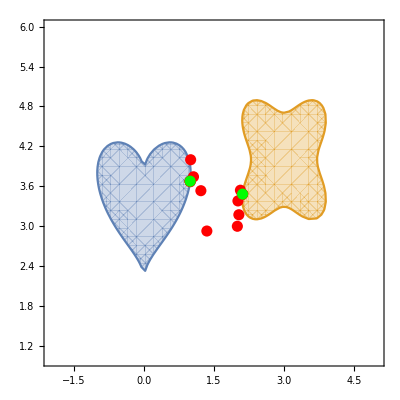

```mathematica
Show[mapa,
Graphics[{Red,PointSize[0.02],Point[#]}]&/@history1⟦;;-2⟧,
Graphics[{Green,PointSize[0.02],Point[#]}]&/@history1⟦{-1}⟧,Graphics[{Red,PointSize[0.02],Point[#]}]&/@history2⟦;;-2⟧,
Graphics[{Green,PointSize[0.02],Point[#]}]&/@history2⟦{-1}⟧
]
```

## Velké sjednocení!!!!!!

```mathematica
Show[mapa,Graphics[{Green,PointSize[0.02],Point[#]}]&/@history1⟦{-1}⟧,Graphics[{Green,PointSize[0.02],Point[#]}]&/@history2⟦{-1}⟧,Graphics[Line[{{x1,x2},{y1,y2}}]]]
```

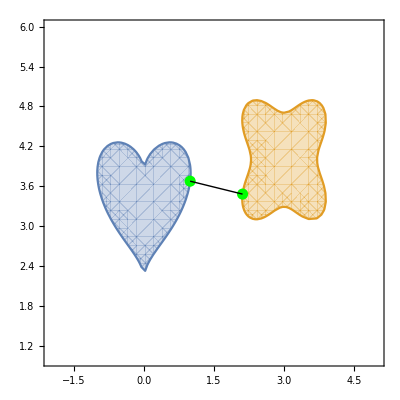

## Provázek a kámen

## Konstanty, počáteční nastavení a tvar kamene

```mathematica
k:=1;g:=-1;h:=1/n;ρ:=0.001;n:=20
s[x_]=0.96-0.25(x-0.5)^2
```

0.96-0.25 (-0.5+x)^2

```mathematica
yvec=Table[Subscript[y, i],{i,1,n-1}];
λvec=Table[Subscript[λ, i],{i,1,n-1}];
xs:=Table[(1/n)i,{i,1,n-1}]
```

## Rovnice a využití Newtonovy metody

```mathematica
Eq1:={Piecewise[{{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1+λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]]),λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])≤0},{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1,λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])>0}}]};
Eqn:={Piecewise[{{(-1+2*yvec[[n-1]]-yvec[[n-2]])/h^2+1+λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]]),λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])≤0},{(-1+2*yvec[[n-1]]-yvec[[n-2]])/h^2+1,λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])>0}}]};
Eqs1:=Table[Piecewise[{{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1+λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]]),λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,2,n-2}];
Eqs2:=Table[Piecewise[{{yvec[[i]]-s[xs[[i]]], λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{-λvec[[i]]/ρ,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,1,n-1}]
```

```mathematica
DfDy=Join[Eq1,Eqs1,Eqn,Eqs2];
D2fDyy=D[ DfDy,{Join[yvec,λvec],1} ];
Table[Subscript[y, i]=1,{i,1,n-1}];Table[Subscript[λ, i]=0,{i,1,n-1}];
i=0;
While[ Sqrt[DfDy.DfDy]>10^-8&&i≤25,
dy=-Inverse[D2fDyy].DfDy;
Table[Subscript[y, i]=Subscript[y, i]+dy[[i]],{i,1,n-1}];
Table[Subscript[λ, i]=Subscript[λ, i]+dy[[n-1+i]],{i,1,n-1}];
i=i+1;
];
```

```mathematica
D2fDyy//MatrixForm
```

(800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800.001 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | -400 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -400 | 800 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000.)

## Jak se provázek nakonec zachová?

```mathematica
xplot:=Join[{0},xs,{1}];yplot:=Join[{1},yvec,{1}];
str:=ListLinePlot[Transpose[{xplot,yplot}],Frame->True,PlotStyle->{Orange}];
st:=RegionPlot[{y<s[x]&&y≥0},{x,0,1},{y,0,1},ColorFunction->Function[{x,y},ColorData["PigeonTones"][Sin[x]Sin[y]]],BoundaryStyle->None];
st2:=RegionPlot[{y<s[x]&&y≥0},{x,0,1},{y,0.85,1},ColorFunction->Function[{x,y},ColorData["PigeonTones"][Sin[x]Sin[y]]],BoundaryStyle->None]
```

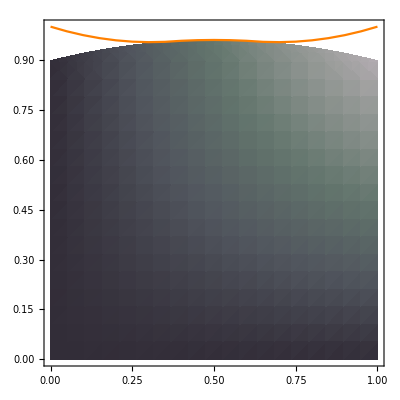

```mathematica
Show[st,str,AspectRatio->1,PlotRange->All]
```

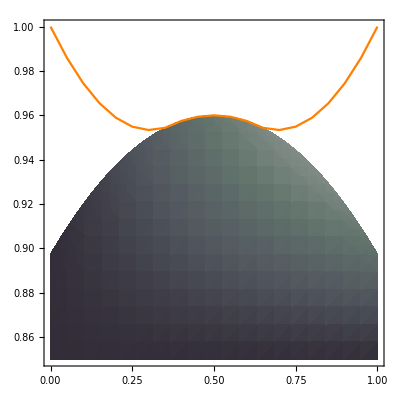

```mathematica
Show[st2,str]
```